## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

```mathematica
numsamples=All; (*number of samples to take for error estimates. Set to "All" if not in debug-mode!*)
```

The following line sets up blocking during the creation of Jackknife samples with block size 1.

```mathematica
MakeJacknifeSamplesB[x_]:=MakeJacknifeSamples[x,1];
```

```mathematica
thisquarkchannel="u-d";
```

## Constants

```mathematica
scalingNat = .1973270524; (* this is GeV*fm *)
```

```mathematica
quarkchannelshort[quarkchannel_]:=Switch[quarkchannel,"up","U","down","D","u-d","UminusD",_,Message["INVALID QUARK CHANNEL"]];
```

```mathematica
basedatapath="/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/

```mathematica
exportdatapath[quarkchannel_]:=basedatapath<>quarkchannelshort[quarkchannel]<>"_";
```

```mathematica
resamplingext="_"<>"jn";
```

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
platdb1=BIDATEXReader[exportdatapath[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

```mathematica
MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sinkMom]//Union
```

{{-1,0,0}}

```mathematica
v1[v3_]:=v3*0.303;
vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb1,MemDBSelect[platdb1,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
(*Print[vlinksv3];*)
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
(*Print[vvectoranddata//OutputForm];
Print[groupSamev//OutputForm];*)
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 7]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 8]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 9]//OutputForm]
Print[vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = 10]//OutputForm]
```

-6
⟨-360(740) × 10  ⟩_(2902J)

-6
⟨-830(730) × 10  ⟩_(2902J)

-6
⟨-930(650) × 10  ⟩_(2902J)

⟨-0.00137(60)⟩_(2902J)

```mathematica
(*xdata = {1,2,3,4,5,6,7,8,9,10};
ydata =Table[vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = {2,2,2,2,2,2,2}, eta = etav], {etav, xdata}]
fit = ResamplingFit2D[xdata,ydata,A*Exp[-B*v],v,{A, B}]
Print[fit[[1]]//OutputForm]
fitpara = fitSamples/.fit
fitA= fitpara[[All,2]][[All,1]]
fitB= fitpara[[All,2]][[All,2]]*)
```

```mathematica
AllLinkPathList = MemDBGet[platdb1,MemDBSelect[platdb1,{gammaValue->8,numberFilter->Re}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
(*Do[Print[i,") ",PathToShift[DistinctLinkPaths[[i+1]],3],"<------->",DistinctLinkPaths[[i+1]], "<------->", MemDBGet[platdb1,MemDBSelect[platdb1,{linkPath->DistinctLinkPaths[[i+1]]}],sideNum]//DeleteDuplicates],{i,CountDistinct[AllLinkPathList]-1}]*)
Print["linkPaths -> {} are skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]]}],{i,CountDistinct[AllLinkPathList]-1}]
(*bveclinkPathsideNumLIST//MatrixForm*)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1list= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 7225

Total No. Distinct linkPath = 87

linkPaths -> {} are skipped

b2 = {-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

b1 = {-8,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,8}

({0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2})

({1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1})

({-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1})

14

36

36

✓ Checked: linkPaths corresponding to   are found

```mathematica
Print["From NucleonEnergy dataset"]
NEdb1=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_1/NucleonEnergy_jn.bidatex"]
latticeP0=MemDBGet[NEdb1,MemDBSelect[NEdb1,{}],energy][[1]];
latticeP1=(latticeP0/latticeP0)*((2*Pi)/(32));
latticePplus=(latticeP1+latticeP0)/Sqrt[2];
latticeMsquare =(latticeP0*latticeP0)-(latticeP1*latticeP1);
latticeM =Sqrt[latticeMsquare];
Print[" = E = (", latticeP0//OutputForm,")"]
Print[" =  = (", latticeP1//OutputForm,")"]
Print[" =  = (", latticePplus//OutputForm,")"]
Print["  = (", latticeM//OutputForm,")"]
```

From NucleonEnergy dataset

< -MemDB- {gammaValue,operation,section,sinkMom,sourceType,comment,tSource,sideLinks,linkPath,sideNum,sideExtent,correlatorType,seqPropNum,tSink,momTransfer,latsizeOrig,latsizeChopped,baryonObservableNr,aBDBIndex,data,numberFilter,energy,chisqrPDOF}>

= E = (⟨0.6530(27)⟩_(2902J))

=  = (⟨0.19634954081957(56)⟩_(2902J))

=  = (⟨0.6006(19)⟩_(2902J))

= (⟨0.6228(28)⟩_(2902J))

```mathematica
GiveTablePlateauEvengPlusImForb[etavalue_]:=(
a=0.114;
S3=1;
TablePlateauEvengPlusImForb = {};
(*Print["considering only positive b2"];*)
Do[
(*If[ bveclinkPathsideNumLISTforbL0[[i,1]][[2]]<0,Continue[]];*)
bl0g8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
b2valuebL0= bveclinkPathsideNumLISTforbL0[[i,1]][[2]];

bl0A12BPplus = ((1/(2*latticeM*S3*b2valuebL0))*((-bl0g1Re/Sqrt[2])-(bl0g8Im/Sqrt[2])+((latticePplus*bl0g3Re)/(0.303023*latticeP0))));

AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbL0[[i,1]],bl0A12BPplus}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

Do[
(*If[ bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]]<0,Continue[]];*)

blPg8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg2Re = vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
b2valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]];
b1valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]];

blNg8Im=vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg1Re=vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg2Re=vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg3Re=vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
b2valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[2]];
b1valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]];

blPA12BPplus =(1/(Sqrt[2]*2*latticeM*S3*b2valuebLP))*((-blPg1Re/2)-(blPg8Im)-((b2valuebLP*blPg2Re)/(2*b1valuebLP))+((latticeP1*blPg3Re)/(2*0.303023*latticeP0)));
blNA12BPplus = (1/(Sqrt[2]*2*latticeM*S3*b2valuebLN))*((-blNg1Re/2)-(blNg8Im)-((b2valuebLN*blNg2Re)/(2*b1valuebLN))+((latticeP1*blNg3Re)/(2*0.303023*latticeP0)));
blEvengPlusImEta = (blPA12BPplus+blNA12BPplus)/2;

AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLpositive[[i,1]],blEvengPlusImEta}];
AppendTo[TablePlateauEvengPlusImForb,{bveclinkPathsideNumLISTforbLnegative[[i,1]],blEvengPlusImEta}];
  ,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
Return[TablePlateauEvengPlusImForb];
)
```

```mathematica
PlotA12B[etavalue_]:=(
TablePlateauEvengPlusImForb = GiveTablePlateauEvengPlusImForb[etavalue];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
Print[MakeErrBars[averagedTablePlateauEvengPlusImForb]];
Print["\n etavalue = ", etavalue];
(*Print["✓ Same  with different linkPath are averaged\n"];*)
bTlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,2]]];
bLlist= Union[averagedTablePlateauEvengPlusImForb[[All,1]][[All,1]]];
PlotbLforDiffbTList={};
Do[
PlotbL2=Transpose[{Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,1]][[All,1]],Select[averagedTablePlateauEvengPlusImForb, #[[1,2]]==bTlist[[bT]]&][[All,2]]}];
AppendTo[PlotbLforDiffbTList,PlotbL2];
 ,{bT,bTlist}];
(*Print[PlotbLforDiffbTList[[1]]];
Print[MakeErrBars[PlotbLforDiffbTList[[1]]]];*)
PlotbL= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Return[Print[PlotbL]];
)
```

```mathematica
GiveTablePlateauEvengPlusImForb[8]
```

{{{0,1,0},⟨-0.0110(76)⟩_(RowBox[{)},{{0,2,0},⟨-0.0027(16)⟩_(RowBox[{)},{{0,3,0},⟨-950(830) × 10⟩_(RowBox[{)},{{0,4,0},⟨-0.00101(56)⟩_(RowBox[{)},{{0,5,0},⟨-730(400) × 10⟩_(RowBox[{)},{{0,6,0},⟨-590(330) × 10⟩_(RowBox[{)},{{0,7,0},⟨-460(270) × 10⟩_(RowBox[{)},{{0,-1,0},⟨-0.0142(77)⟩_(RowBox[{)},{{0,-2,0},⟨-0.0038(16)⟩_(RowBox[{)},{{0,-3,0},⟨-990(800) × 10⟩_(RowBox[{)},{{0,-4,0},⟨-650(530) × 10⟩_(RowBox[{)},{{0,-5,0},⟨-0.00008 ± 0.00037⟩_(RowBox[{)},{{0,-6,0},⟨-0.00004 ± 0.00029⟩_(RowBox[{)},{{0,-7,0},⟨-0.00002 ± 0.00023⟩_(RowBox[{)},{{1,1,0},⟨-0.0084(17)⟩_(RowBox[{)},{{-1,1,0},⟨-0.0084(17)⟩_(RowBox[{)},{{2,2,0},⟨-0.00143(29)⟩_(RowBox[{)},{{-2,2,0},⟨-0.00143(29)⟩_(RowBox[{)},{{3,3,0},⟨-480(160) × 10⟩_(RowBox[{)},{{-3,3,0},⟨-480(160) × 10⟩_(RowBox[{)},{{4,4,0},⟨-320(110) × 10⟩_(RowBox[{)},{{-4,4,0},⟨-320(110) × 10⟩_(RowBox[{)},{{5,5,0},⟨-143(70) × 10⟩_(RowBox[{)},{{-5,5,0},⟨-143(70) × 10⟩_(RowBox[{)},{{1,1,0},⟨-0.0084(17)⟩_(RowBox[{)},{{-1,1,0},⟨-0.0084(17)⟩_(RowBox[{)},{{2,2,0},⟨-0.00148(28)⟩_(RowBox[{)},{{-2,2,0},⟨-0.00148(28)⟩_(RowBox[{)},{{3,3,0},⟨-470(160) × 10⟩_(RowBox[{)},{{-3,3,0},⟨-470(160) × 10⟩_(RowBox[{)},{{4,4,0},⟨-290(110) × 10⟩_(RowBox[{)},{{-4,4,0},⟨-290(110) × 10⟩_(RowBox[{)},{{5,5,0},⟨-171(71) × 10⟩_(RowBox[{)},{{-5,5,0},⟨-171(71) × 10⟩_(RowBox[{)},{{1,2,0},⟨-0.00265(41)⟩_(RowBox[{)},{{-1,2,0},⟨-0.00265(41)⟩_(RowBox[{)},{{2,4,0},⟨-410(140) × 10⟩_(RowBox[{)},{{-2,4,0},⟨-410(140) × 10⟩_(RowBox[{)},{{3,6,0},⟨-196(72) × 10⟩_(RowBox[{)},{{-3,6,0},⟨-196(72) × 10⟩_(RowBox[{)},{{2,1,0},⟨-0.00336(74)⟩_(RowBox[{)},{{-2,1,0},⟨-0.00336(74)⟩_(RowBox[{)},{{4,2,0},⟨-320(220) × 10⟩_(RowBox[{)},{{-4,2,0},⟨-320(220) × 10⟩_(RowBox[{)},{{6,3,0},⟨-240(120) × 10⟩_(RowBox[{)},{{-6,3,0},⟨-240(120) × 10⟩_(RowBox[{)},{{4,1,0},⟨-150(430) × 10⟩_(RowBox[{)},{{-4,1,0},⟨-150(430) × 10⟩_(RowBox[{)},{{8,2,0},⟨140(170) × 10⟩_(RowBox[{)},{{-8,2,0},⟨140(170) × 10⟩_(RowBox[{)},{{1,-1,0},⟨-0.0081(18)⟩_(RowBox[{)},{{-1,-1,0},⟨-0.0081(18)⟩_(RowBox[{)},{{2,-2,0},⟨-0.00189(31)⟩_(RowBox[{)},{{-2,-2,0},⟨-0.00189(31)⟩_(RowBox[{)},{{3,-3,0},⟨-210(160) × 10⟩_(RowBox[{)},{{-3,-3,0},⟨-210(160) × 10⟩_(RowBox[{)},{{4,-4,0},⟨26(96) × 10⟩_(RowBox[{)},{{-4,-4,0},⟨26(96) × 10⟩_(RowBox[{)},{{5,-5,0},⟨29(73) × 10⟩_(RowBox[{)},{{-5,-5,0},⟨29(73) × 10⟩_(RowBox[{)},{{1,-1,0},⟨-0.0080(18)⟩_(RowBox[{)},{{-1,-1,0},⟨-0.0080(18)⟩_(RowBox[{)},{{2,-2,0},⟨-0.00178(31)⟩_(RowBox[{)},{{-2,-2,0},⟨-0.00178(31)⟩_(RowBox[{)},{{3,-3,0},⟨-140(160) × 10⟩_(RowBox[{)},{{-3,-3,0},⟨-140(160) × 10⟩_(RowBox[{)},{{4,-4,0},⟨0.00003 ± 0.0001⟩_(RowBox[{)},{{-4,-4,0},⟨0.00003 ± 0.0001⟩_(RowBox[{)},{{5,-5,0},⟨43(76) × 10⟩_(RowBox[{)},{{-5,-5,0},⟨43(76) × 10⟩_(RowBox[{)},{{1,-2,0},⟨-0.00320(44)⟩_(RowBox[{)},{{-1,-2,0},⟨-0.00320(44)⟩_(RowBox[{)},{{2,-4,0},⟨-190(140) × 10⟩_(RowBox[{)},{{-2,-4,0},⟨-190(140) × 10⟩_(RowBox[{)},{{3,-6,0},⟨-48(74) × 10⟩_(RowBox[{)},{{-3,-6,0},⟨-48(74) × 10⟩_(RowBox[{)},{{2,-1,0},⟨-0.00343(79)⟩_(RowBox[{)},{{-2,-1,0},⟨-0.00343(79)⟩_(RowBox[{)},{{4,-2,0},⟨-350(220) × 10⟩_(RowBox[{)},{{-4,-2,0},⟨-350(220) × 10⟩_(RowBox[{)},{{6,-3,0},⟨0.00004 ± 0.00011⟩_(RowBox[{)},{{-6,-3,0},⟨0.00004 ± 0.00011⟩_(RowBox[{)},{{4,-1,0},⟨-660(460) × 10⟩_(RowBox[{)},{{-4,-1,0},⟨-660(460) × 10⟩_(RowBox[{)},{{8,-2,0},⟨0.00004 ± 0.00015⟩_(RowBox[{)},{{-8,-2,0},⟨0.00004 ± 0.00015⟩_(RowBox[{)}}

{{{{0,1,0},-0.0109936},ErrorBar[{-0.0075437,0.0075437}]},{{{0,2,0},-0.00268132},ErrorBar[{-0.00156385,0.00156385}]},{{{0,3,0},-0.000945924},ErrorBar[{-0.000825553,0.000825553}]},{{{0,4,0},-0.00101082},ErrorBar[{-0.000551222,0.000551222}]},{{{0,5,0},-0.000730793},ErrorBar[{-0.00039562,0.00039562}]},{{{0,6,0},-0.00058886},ErrorBar[{-0.000322714,0.000322714}]},{{{0,7,0},-0.000457913},ErrorBar[{-0.000261933,0.000261933}]},{{{0,-1,0},-0.0142069},ErrorBar[{-0.00763936,0.00763936}]},{{{0,-2,0},-0.00375458},ErrorBar[{-0.00152789,0.00152789}]},{{{0,-3,0},-0.000992697},ErrorBar[{-0.00079911,0.00079911}]},{{{0,-4,0},-0.000651205},ErrorBar[{-0.000528881,0.000528881}]},{{{0,-5,0},-0.0000830307},ErrorBar[{-0.000365201,0.000365201}]},{{{0,-6,0},-0.0000378167},ErrorBar[{-0.000289847,0.000289847}]},{{{0,-7,0},-0.0000221486},ErrorBar[{-0.000229187,0.000229187}]},{{{1,1,0},-0.00843467},ErrorBar[{-0.00163764,0.00163764}]},{{{-1,1,0},-0.00843467},ErrorBar[{-0.00163764,0.00163764}]},{{{2,2,0},-0.00145496},ErrorBar[{-0.000275713,0.000275713}]},{{{-2,2,0},-0.00145496},ErrorBar[{-0.000275713,0.000275713}]},{{{3,3,0},-0.000471098},ErrorBar[{-0.000149232,0.000149232}]},{{{-3,3,0},-0.000471098},ErrorBar[{-0.000149232,0.000149232}]},{{{4,4,0},-0.00030101},ErrorBar[{-0.000101075,0.000101075}]},{{{-4,4,0},-0.00030101},ErrorBar[{-0.000101075,0.000101075}]},{{{5,5,0},-0.000157161},ErrorBar[{-0.0000666933,0.0000666933}]},{{{-5,5,0},-0.000157161},ErrorBar[{-0.0000666933,0.0000666933}]},{{{1,2,0},-0.00265321},ErrorBar[{-0.000408058,0.000408058}]},{{{-1,2,0},-0.00265321},ErrorBar[{-0.000408058,0.000408058}]},{{{2,4,0},-0.000411297},ErrorBar[{-0.00013598,0.00013598}]},{{{-2,4,0},-0.000411297},ErrorBar[{-0.00013598,0.00013598}]},{{{3,6,0},-0.000196429},ErrorBar[{-0.0000710788,0.0000710788}]},{{{-3,6,0},-0.000196429},ErrorBar[{-0.0000710788,0.0000710788}]},{{{2,1,0},-0.0033641},ErrorBar[{-0.00073724,0.00073724}]},{{{-2,1,0},-0.0033641},ErrorBar[{-0.00073724,0.00073724}]},{{{4,2,0},-0.000320757},ErrorBar[{-0.000214822,0.000214822}]},{{{-4,2,0},-0.000320757},ErrorBar[{-0.000214822,0.000214822}]},{{{6,3,0},-0.000240461},ErrorBar[{-0.000116841,0.000116841}]},{{{-6,3,0},-0.000240461},ErrorBar[{-0.000116841,0.000116841}]},{{{4,1,0},-0.000151603},ErrorBar[{-0.000421899,0.000421899}]},{{{-4,1,0},-0.000151603},ErrorBar[{-0.000421899,0.000421899}]},{{{8,2,0},0.000142791},ErrorBar[{-0.000164907,0.000164907}]},{{{-8,2,0},0.000142791},ErrorBar[{-0.000164907,0.000164907}]},{{{1,-1,0},-0.00805716},ErrorBar[{-0.00171698,0.00171698}]},{{{-1,-1,0},-0.00805716},ErrorBar[{-0.00171698,0.00171698}]},{{{2,-2,0},-0.00183121},ErrorBar[{-0.000302394,0.000302394}]},{{{-2,-2,0},-0.00183121},ErrorBar[{-0.000302394,0.000302394}]},{{{3,-3,0},-0.000179312},ErrorBar[{-0.000153468,0.000153468}]},{{{-3,-3,0},-0.000179312},ErrorBar[{-0.000153468,0.000153468}]},{{{4,-4,0},0.0000296225},ErrorBar[{-0.0000940692,0.0000940692}]},{{{-4,-4,0},0.0000296225},ErrorBar[{-0.0000940692,0.0000940692}]},{{{5,-5,0},0.0000359608},ErrorBar[{-0.000070866,0.000070866}]},{{{-5,-5,0},0.0000359608},ErrorBar[{-0.000070866,0.000070866}]},{{{1,-2,0},-0.00320065},ErrorBar[{-0.000434071,0.000434071}]},{{{-1,-2,0},-0.00320065},ErrorBar[{-0.000434071,0.000434071}]},{{{2,-4,0},-0.00018593},ErrorBar[{-0.000138126,0.000138126}]},{{{-2,-4,0},-0.00018593},ErrorBar[{-0.000138126,0.000138126}]},{{{3,-6,0},-0.0000482677},ErrorBar[{-0.0000734088,0.0000734088}]},{{{-3,-6,0},-0.0000482677},ErrorBar[{-0.0000734088,0.0000734088}]},{{{2,-1,0},-0.00343234},ErrorBar[{-0.00078104,0.00078104}]},{{{-2,-1,0},-0.00343234},ErrorBar[{-0.00078104,0.00078104}]},{{{4,-2,0},-0.000354799},ErrorBar[{-0.000212367,0.000212367}]},{{{-4,-2,0},-0.000354799},ErrorBar[{-0.000212367,0.000212367}]},{{{6,-3,0},0.0000387758},ErrorBar[{-0.000109622,0.000109622}]},{{{-6,-3,0},0.0000387758},ErrorBar[{-0.000109622,0.000109622}]},{{{4,-1,0},-0.000661472},ErrorBar[{-0.000457093,0.000457093}]},{{{-4,-1,0},-0.000661472},ErrorBar[{-0.000457093,0.000457093}]},{{{8,-2,0},0.0000424447},ErrorBar[{-0.00015442,0.00015442}]},{{{-8,-2,0},0.0000424447},ErrorBar[{-0.00015442,0.00015442}]}}

etavalue = 8

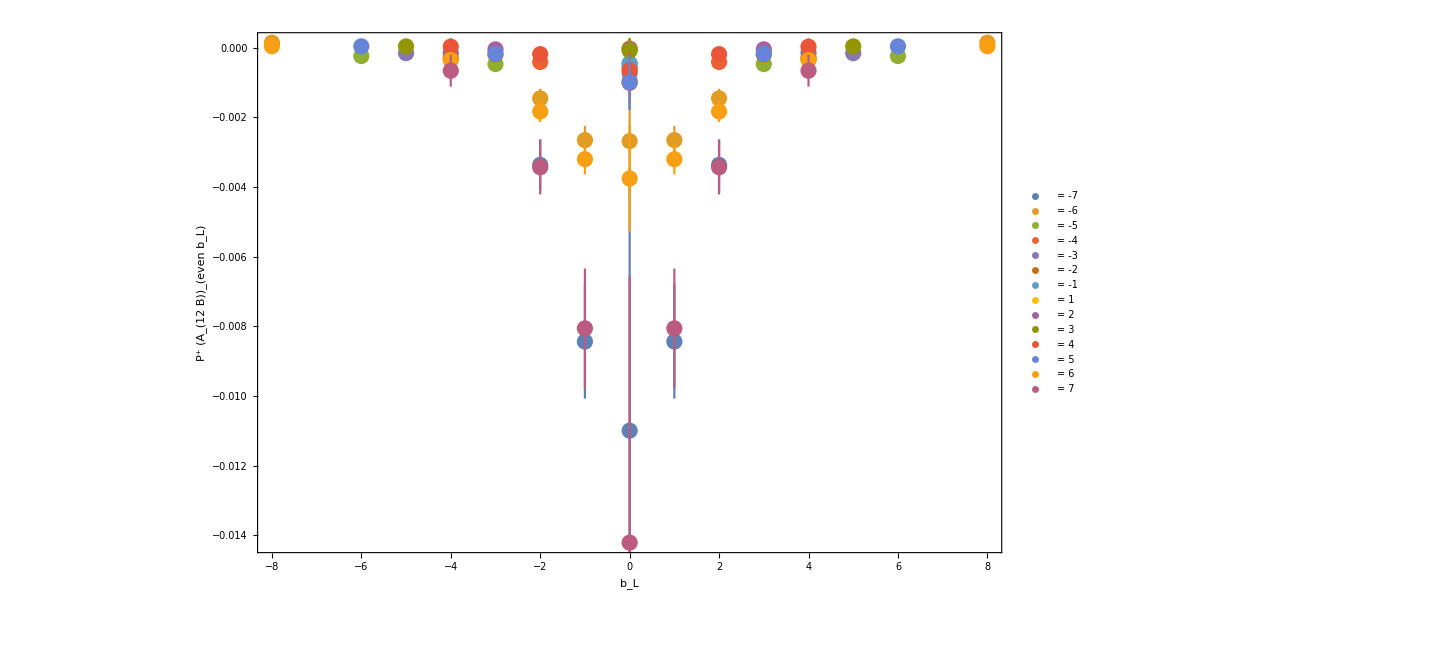

```mathematica
PlotA12B[8]
```

```mathematica
etabvalueerrA12B[etavalue_]:=(
etaaveragedTablePlateauEvengPlusImForb={};
TablePlateauEvengPlusImForb = GiveTablePlateauEvengPlusImForb[etavalue];
groupSameb=GroupBy[TablePlateauEvengPlusImForb,First->Last];
averagedTablePlateauEvengPlusImForb=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSameb];
bvalueerrbar = MakeErrBars[averagedTablePlateauEvengPlusImForb];
Do[
AppendTo[etaaveragedTablePlateauEvengPlusImForb, {etavalue, bvalueerrbar[[i]][[1]][[1]][[1]] ,bvalueerrbar[[i]][[1]][[1]][[2]],  bvalueerrbar[[i]][[1]][[2]],  bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[bvalueerrbar]}];
Return[etaaveragedTablePlateauEvengPlusImForb]
)
etabvalueerrA12B[8]
```

{{8,0,1,-0.0109936,0.0075437},{8,0,2,-0.00268132,0.00156385},{8,0,3,-0.000945924,0.000825553},{8,0,4,-0.00101082,0.000551222},{8,0,5,-0.000730793,0.00039562},{8,0,6,-0.00058886,0.000322714},{8,0,7,-0.000457913,0.000261933},{8,0,-1,-0.0142069,0.00763936},{8,0,-2,-0.00375458,0.00152789},{8,0,-3,-0.000992697,0.00079911},{8,0,-4,-0.000651205,0.000528881},{8,0,-5,-0.0000830307,0.000365201},{8,0,-6,-0.0000378167,0.000289847},{8,0,-7,-0.0000221486,0.000229187},{8,1,1,-0.00843467,0.00163764},{8,-1,1,-0.00843467,0.00163764},{8,2,2,-0.00145496,0.000275713},{8,-2,2,-0.00145496,0.000275713},{8,3,3,-0.000471098,0.000149232},{8,-3,3,-0.000471098,0.000149232},{8,4,4,-0.00030101,0.000101075},{8,-4,4,-0.00030101,0.000101075},{8,5,5,-0.000157161,0.0000666933},{8,-5,5,-0.000157161,0.0000666933},{8,1,2,-0.00265321,0.000408058},{8,-1,2,-0.00265321,0.000408058},{8,2,4,-0.000411297,0.00013598},{8,-2,4,-0.000411297,0.00013598},{8,3,6,-0.000196429,0.0000710788},{8,-3,6,-0.000196429,0.0000710788},{8,2,1,-0.0033641,0.00073724},{8,-2,1,-0.0033641,0.00073724},{8,4,2,-0.000320757,0.000214822},{8,-4,2,-0.000320757,0.000214822},{8,6,3,-0.000240461,0.000116841},{8,-6,3,-0.000240461,0.000116841},{8,4,1,-0.000151603,0.000421899},{8,-4,1,-0.000151603,0.000421899},{8,8,2,0.000142791,0.000164907},{8,-8,2,0.000142791,0.000164907},{8,1,-1,-0.00805716,0.00171698},{8,-1,-1,-0.00805716,0.00171698},{8,2,-2,-0.00183121,0.000302394},{8,-2,-2,-0.00183121,0.000302394},{8,3,-3,-0.000179312,0.000153468},{8,-3,-3,-0.000179312,0.000153468},{8,4,-4,0.0000296225,0.0000940692},{8,-4,-4,0.0000296225,0.0000940692},{8,5,-5,0.0000359608,0.000070866},{8,-5,-5,0.0000359608,0.000070866},{8,1,-2,-0.00320065,0.000434071},{8,-1,-2,-0.00320065,0.000434071},{8,2,-4,-0.00018593,0.000138126},{8,-2,-4,-0.00018593,0.000138126},{8,3,-6,-0.0000482677,0.0000734088},{8,-3,-6,-0.0000482677,0.0000734088},{8,2,-1,-0.00343234,0.00078104},{8,-2,-1,-0.00343234,0.00078104},{8,4,-2,-0.000354799,0.000212367},{8,-4,-2,-0.000354799,0.000212367},{8,6,-3,0.0000387758,0.000109622},{8,-6,-3,0.0000387758,0.000109622},{8,4,-1,-0.000661472,0.000457093},{8,-4,-1,-0.000661472,0.000457093},{8,8,-2,0.0000424447,0.00015442},{8,-8,-2,0.0000424447,0.00015442}}

```mathematica
Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_A12B_err_wt_NEnergyJakkif.h5",Table["eta_"<>ToString[n]<>"_bL_bT_A12B_err"->etabvalueerrA12B[n],{n,1,10}]]
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_A12B_err_wt_NEnergyJakkif.h5

```mathematica
Import["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_bL_bT_A12B_err_wt_NEnergyJakkif.h5","StructureGraph"]
```

-Graphics-

```mathematica
(*datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
Print[datafor2dGaussianFitbLbTerrors]

fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```